```mathematica
HexBasis = {{1,0},{1/2,Sqrt[3]/2}}
```

{{1,0},{1/2,(√3)/2}}

```mathematica
MakeGrid[size_,xoffset_, yoffset_] := TranslationTransform[{xoffset,yoffset}] /@ Flatten[Table[{x,y}, {x, -size, size}, {y, -size, size}] ,1]
MakeGrid[2]
```

{{-2,-5/3},{-2,-2/3},{-2,1/3},{-2,4/3},{-2,7/3},{-1,-5/3},{-1,-2/3},{-1,1/3},{-1,4/3},{-1,7/3},{0,-5/3},{0,-2/3},{0,1/3},{0,4/3},{0,7/3},{1,-5/3},{1,-2/3},{1,1/3},{1,4/3},{1,7/3},{2,-5/3},{2,-2/3},{2,1/3},{2,4/3},{2,7/3}}

Use dot product to multiple each point by a basis vector, to turn a square grid into a triangular one

```mathematica
Dot[MakeGrid[2],HexBasis ]
```

{{-3,-√3},{-5/2,-(√3)/2},{-2,0},{-3/2,(√3)/2},{-1,√3},{-2,-√3},{-3/2,-(√3)/2},{-1,0},{-1/2,(√3)/2},{0,√3},{-1,-√3},{-1/2,-(√3)/2},{0,0},{1/2,(√3)/2},{1,√3},{0,-√3},{1/2,-(√3)/2},{1,0},{3/2,(√3)/2},{2,√3},{1,-√3},{3/2,-(√3)/2},{2,0},{5/2,(√3)/2},{3,√3}}

A neat way to select “every other” element is to add x and y and check if it’s even or odd. TODO: how would I delete just the points that would leave me with honeycomb?

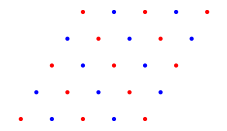

```mathematica
Graphics[{
{Red, Point /@ Dot[
Select[EvenQ[Plus @@ #]&] @ MakeGrid[2],
HexBasis
]},
{Blue, Point /@ Dot[
Select[OddQ[Plus @@ #]&] @ MakeGrid[2],
HexBasis
]}
}]
```

Next, I want to start with the point at 0,0 and calculate the norm out to each point, so I can group the points into orbital ‘neighborhoods’ and count how many neighbors each one has.

```mathematica
CountsBy[MakeGrid[4], Norm]
CountsBy[MakeGrid[128], Norm] // Values // Union
```

<|(√265)/3→2,(4 √13)/3→2,13/3→3,(2 √37)/3→2,(√145)/3→4,(4 √10)/3→2,(√193)/3→2,(2 √61)/3→2,(√313)/3→2,(√202)/3→2,(√106)/3→2,(√85)/3→4,(√82)/3→2,(√97)/3→2,(√130)/3→4,(√181)/3→2,(5 √10)/3→2,(√157)/3→2,10/3→3,(√61)/3→2,(2 √10)/3→2,(√37)/3→2,(2 √13)/3→2,(2 √34)/3→2,(√205)/3→2,(√73)/3→2,(√34)/3→2,(√13)/3→2,(√10)/3→2,5/3→3,(√58)/3→2,(√109)/3→2,(√178)/3→2,11/3→1,8/3→1,2/3→1,1/3→1,4/3→1,7/3→1|>

{1,2,3,4,5,6,7,8,9,10,12,14,15,16,18}

```mathematica
CountsBy[Dot[MakeGrid[4],HexBasis], Norm]
CountsBy[Dot[MakeGrid[60],HexBasis], Norm] // Values // Union
```

<|(√397)/3→1,(4 √19)/3→1,(√229)/3→1,(2 √43)/3→1,(√133)/3→4,(4 √7)/3→2,(√109)/3→2,(2 √31)/3→2,(√157)/3→2,(√301)/3→1,(√217)/3→2,(√151)/3→1,(√103)/3→2,(√73)/3→2,(√61)/3→2,(√67)/3→2,(√91)/3→4,(√223)/3→1,(2 √37)/3→1,(2 √13)/3→2,(√31)/3→2,(2 √7)/3→2,(√43)/3→2,(2 √19)/3→2,(√127)/3→2,(√163)/3→1,(√97)/3→2,7/3→3,(√19)/3→2,(√7)/3→2,(√13)/3→2,(√37)/3→2,(√79)/3→2,(√139)/3→2,11/3→1,8/3→1,5/3→1,2/3→1,1/3→1,4/3→1,10/3→1,13/3→1,14/3→1,(√283)/3→1,(√193)/3→1,(√271)/3→1,(√367)/3→1,(4 √13)/3→1,(√277)/3→1,(2 √91)/3→1,(√469)/3→1|>

{1,2,3,4,5,6,7,8,9,12}

Drawing some circles with a radius equal to each of the norms

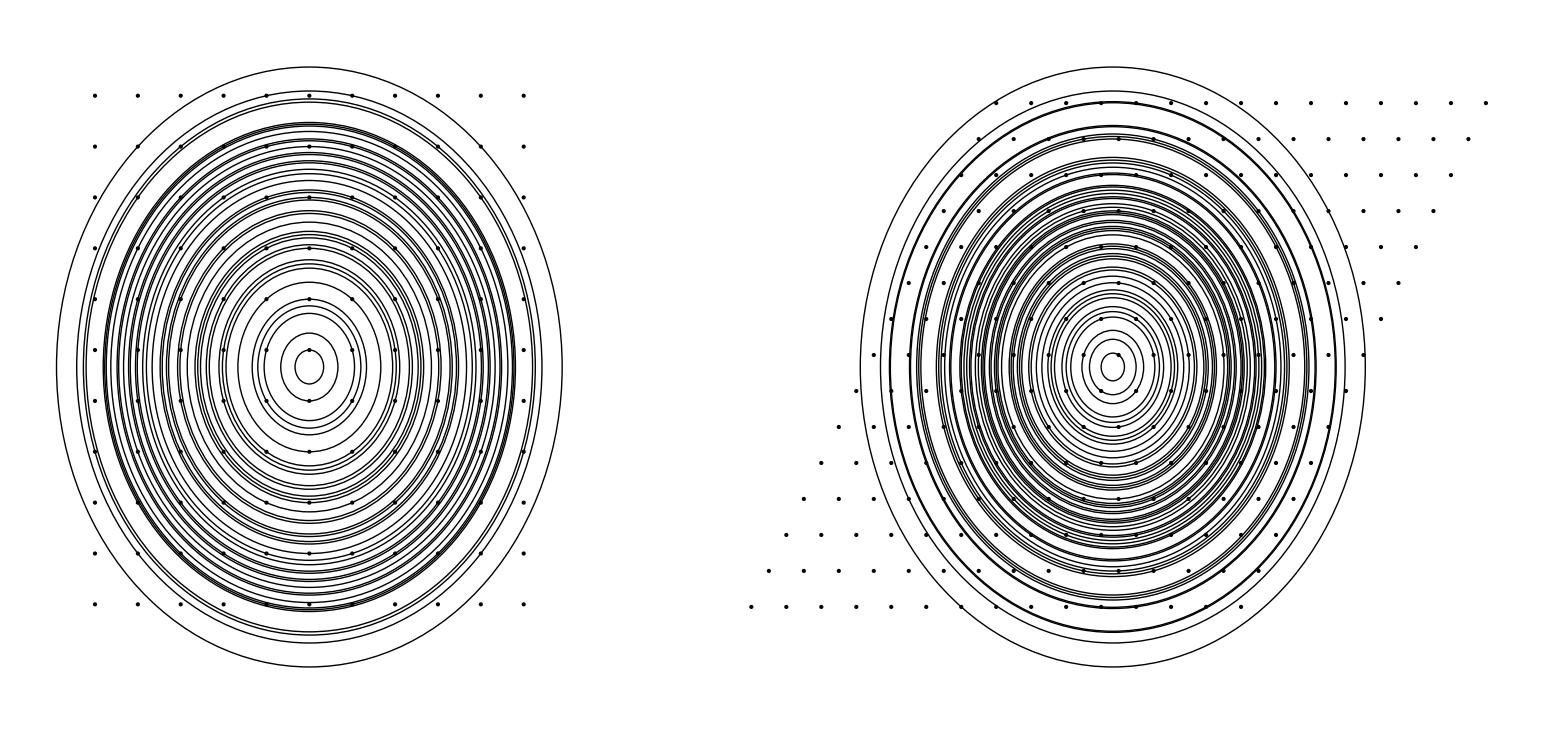

```mathematica
GraphicsRow[{
Graphics[{
{PointSize[Medium], Point /@ MakeGrid[5]},
Circle[{0,0}, #] & /@ Union[ Norm /@ MakeGrid[4]]
}],Graphics[{
{PointSize[Medium], Point /@ (MakeGrid[7].HexBasis)},
Circle[{0,0}, #] & /@ Union[ Norm /@ (MakeGrid[4].HexBasis)]
}]
}]
```

DensityPlot[Abs[Subtract[x,First@Nearest[squarednorms, x]]] , {x,0, 9}, {y, 0, 1}, MaxRecursion→ 7, PlotTheme->”Monochrome”

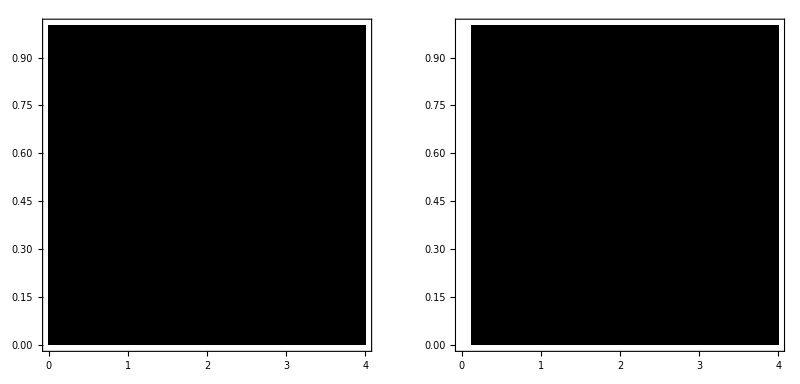

```mathematica
GraphicsRow[{
DensityPlot[
Abs[Subtract[
x,
First@Nearest[Union[Norm/@MakeGrid[3]],x]
]], 
{x,0, 4}, {y, 0, 1},MaxRecursion-> 4, PlotTheme->"Monochrome"],
DensityPlot[
Abs[Subtract[
x,
First@Nearest[Union[Norm/@(MakeGrid[3].HexBasis)],x]
]], 
{x,0, 4}, {y, 0, 1},MaxRecursion-> 4, PlotTheme->"Monochrome"]
}]
```

```mathematica
DrawMandala[range_, d_, j_, k_] := Module[
{
squaregrid = MakeGrid[Round@range, j, k],
shellcount = CountsBy[ MakeGrid[Round@range, j, k], Norm] ,
density =1 / (Sqrt[range] * (100 + range))
},
Graphics[{
PointSize[d * density*(shellcount[Norm[#]])],
Point[#]
} & /@ squaregrid,
PlotRange-> 4range /5,
ImageSize->Medium
]]
```

```mathematica
Manipulate[DrawMandala[n,d, j,k], {n,5, 50, .1}, {d, 0, 10, .1}, {j, 0, 1, Sqrt[3]/12}, {k, 0, 1,Sqrt[3]/12}]
```

```mathematica
ExportVideo["squaremandala5to25", 30, Table[DrawMandala[n], {n,5, 25, 1/15}]]
```

CreateDirectory::filex: C:\Users\cjack\Documents\squaremandala5to25 already exists.

```mathematica
DrawHexMandala[range_] := Module[
{
squaregrid = MakeGrid[Round@range].HexBasis,
shellcount = CountsBy[ MakeGrid[Round@range].HexBasis, Norm] ,
density =1 / (Sqrt[range] * (180 + range))
},
Graphics[{
PointSize[density*(shellcount[Norm[#]])],
Point[#]
} & /@ squaregrid,
PlotRange->  {{-range, range}, {-(9/16) range , (9/16) range  }},
ImageSize->{1920, 1080}
]]
```

```mathematica
1080/1920
```

9/16

```mathematica
Manipulate[DrawHexMandala[n], {n,5, 40, .1}]
```

```mathematica
ExportVideo["hexmandala5to40-highres", 12, Table[DrawHexMandala[n], {n,5, 60, 1/4}]]
```